```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,colorfuncOld,rng,P1,TabFibNew,TabFibNewNewFromPiby2Only]
```

```mathematica
TabFibNew=Import["WSMTabfibnewdata_up+8_dn+6Rationalm=4.dat"];
```

```mathematica
TabFibNew
```

{{1.,-3.14159,0.000243876},{1.9245,-3.14159,0.0007061},{2.4792,-3.14159,0.00186572},{3.4037,-3.14159,0.00260554},3766,{57.2096,3.14159,0.00260559},{57.7643,3.14159,0.00186576},{58.6888,3.14159,0.000706112},{59.6133,3.14159,0.000243875}}
 |  |  |  |

```mathematica
Fibon1D= Import["Fibon1Drational.dat"]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0}}

```mathematica
Dimensions[TabFibNew]
```

{3774,3}

```mathematica
nsiteQuasi = Dimensions[Fibon1D][[1]]
```

74

```mathematica
kzSize = Dimensions[TabFibNew][[1]]/nsiteQuasi
```

51

```mathematica
TabFibNew[[75]]
```

{1.,-3.01593,0.000246052}

```mathematica
Do[TabFibNew[[a*nsiteQuasi +b]][[1]] = b,{a,0,kzSize-1},{b,1,nsiteQuasi}]
```

```mathematica
TabFibNew[[84]]
```

{10,-3.01593,0.0113738}

```mathematica
largestX = Ceiling[Fibon1D[[nsiteQuasi]][[1]]]
```

74

```mathematica
colorfuncOld=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibNew[[All,3]];
```

```mathematica
rng[[2]]
```

0.487326

```mathematica
P1 = BarLegend[{colorfuncOld[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.0"},{rng[[2]]/2,"2.0"},{rng[[2]]-10^-3,"4.0"}}]
```

```mathematica
TabFibNewNewFromPiby2Only = {};
```

```mathematica
Do[If[Abs[TabFibNew[[ii]][[2]]]<π/2,TabFibNewNewFromPiby2Only=Append[TabFibNewNewFromPiby2Only,TabFibNew[[ii]]]],{ii,1,Dimensions[TabFibNew][[1]]}]
```

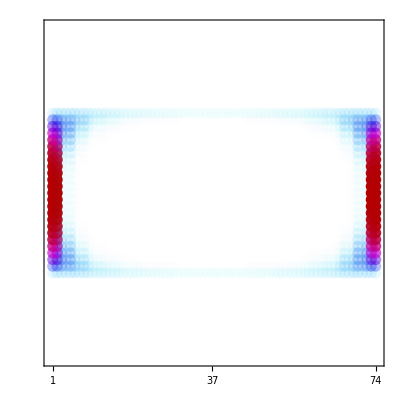

```mathematica
Show[Graphics[{PointSize[0.02],colorfuncOld[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.5,largestX+0.4},{-π,π}}],
FrameTicks->{{{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}},None},{{1,{Ceiling[largestX/2],Ceiling[nsiteQuasi/2]},{largestX,nsiteQuasi}},None}},
ImageSize-> 400,AspectRatio->1,RotateLabel->False,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}}
]
```